```mathematica
LaplaceTransform[(λ t)^(k-1)λ/Gamma[k] E^(-λ t),t,s]
```

λ^k (s+λ)^-k

```mathematica
FullSimplify[λ^k (s+λ)^-k,{s>0,k>0,λ>0}]
```

(λ/(s+λ))^k

n=λ b, a=γ/μ where μ=rate of the Gamma dist.

```mathematica
testsum[a_,n_,k_]:=Exp[-NSum[1/(m a^(k m))(Zeta[k m,1+1/a]-Zeta[k m,n+1+1/a]),{m,1,100},Method->"WynnEpsilon"]]
check[a_,n_,k_]:=Product[1-(1/(m a+1))^k,{m,1,n}]
```

```mathematica
testsum[2,2,2]
```

0.853333

```mathematica
check[2,2,2]//N
```

0.853333

```mathematica
a=2;
k=.3;
tabletest=Table[{x,E^x testsum[a,x,k]},{x,1,20,0.25}];
```

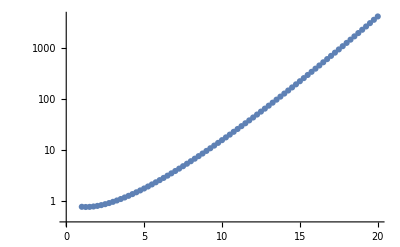

```mathematica
ListLogPlot[tabletest]
```